## Read and Analyse muons_200m.dat

Read the output of the MUSIC muon-propagation simulation through 200 m of water, extract column variables, compute derived quantities, and display kinematic distributions.

```mathematica
SetDirectory["/Users/diwan/Documents/Projects/cosmics/muonsim"]
```

/Users/diwan/Documents/Projects/cosmics/muonsim

```mathematica
?Import
```

### Step 1 — Import the data table (skip comment lines starting with #)

```mathematica
data = Import["muons_200m.dat", "Table"];
n = Length[data];
Print["Loaded ", n, " surviving muons"]
```

Loaded 10002 surviving muons

```mathematica
(* the first two rows are comments to be deleted *)
```

```mathematica
data = Drop[data,2]
```

### Step 2 — Assign named column variables

```mathematica
pmu0 = Part[data, All, 1];
cth0 = Part[data, All, 2];
phi0 = Part[data, All, 3];
emuf = Part[data, All, 4];
xf = Part[data, All, 5];
yf = Part[data, All, 6];
zf = Part[data, All, 7];
cxf = Part[data, All, 8];
cyf = Part[data, All, 9];
czf = Part[data, All, 10];
```

### Step 3 — Derived quantities

```mathematica
rlat = Sqrt[xf^2 + yf^2] / 100.; 
th0 = ArcCos[cth0] * 180. / π;
thf = ArcCos[Clip[czf, {-1., 1.}]] * 180. / π;
```

```mathematica
Mean[thf]
```

32.0133

### Step 4 — Summary statistics

```mathematica
TableForm[
{{"Quantity", "Min", "Mean", "Max"},
{"pmu0 [GeV/c]", Min[pmu0], Mean[pmu0], Max[pmu0]},
{"emu_f [GeV]", Min[emuf], Mean[emuf], Max[emuf]},
{"theta_0 [deg]", Min[th0], Mean[th0], Max[th0]},
{"r_lat [m]", Min[rlat], Mean[rlat], Max[rlat]},
{"theta_f [deg]", Min[thf], Mean[thf], Max[thf]}
}, TableHeadings -> {None, None}
]
```

Quantity | Min | Mean | Max
pmu0 [GeV/c] | 46.1993 | 93.2599 | 294.224
emu_f [GeV] | 0.106771 | 30.5464 | 202.432
theta_0 [deg] | 0.458367 | 31.9825 | 73.4905
r_lat [m] | 1.17083 | 139.782 | 673.801
theta_f [deg] | 0.181185 | 32.0133 | 73.7903

### Step 5 — Kinematic distributions

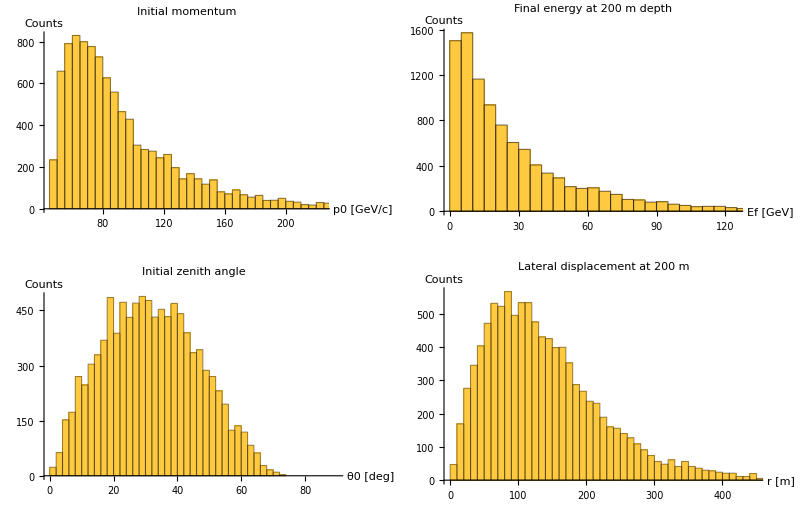

```mathematica
p1 = Histogram[pmu0, 40, "Count", PlotLabel -> "Initial momentum", AxesLabel -> {"p0 [GeV/c]", "Counts"}];
p2 = Histogram[emuf, 50, "Count", PlotLabel -> "Final energy at 200 m depth", AxesLabel -> {"Ef [GeV]", "Counts"}];
p3 = Histogram[th0, {0, 90, 2}, "Count", PlotLabel -> "Initial zenith angle", AxesLabel -> {"θ0 [deg]", "Counts"}];
p4 = Histogram[rlat, 50, "Count", PlotLabel -> "Lateral displacement at 200 m", AxesLabel -> {"r [m]", "Counts"}];
GraphicsGrid[{{p1, p2}, {p3, p4}}, ImageSize -> 800, Spacings -> {0, 20}]
```

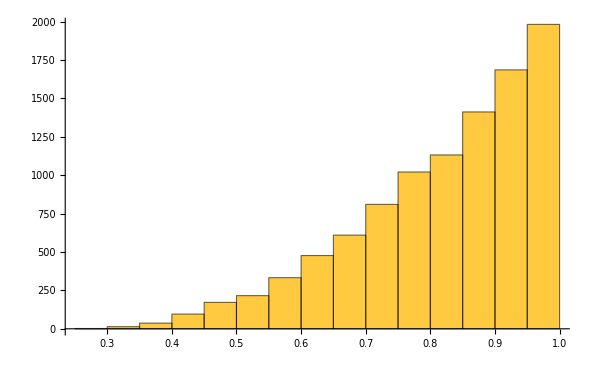

```mathematica
Histogram[cth0]
```

### Step 6 — Export combined figure

```mathematica
Export["muon_distributions.pdf", GraphicsGrid[{{p1, p2}, {p3, p4}}, ImageSize -> 800, Spacings -> {0, 20}]]
```